```mathematica
3^100
```

515377520732011331036461129765621272702107522001

```mathematica
3^1000
```

1322070819480806636890455259752144365965422032752148167664920368226828597346704899540778313850608061963909777696872582355950954582100618911865342725257953674027620225198320803878014774228964841274390400117588618041128947815623094438061566173054086674490506178125480344405547054397038895817465368254916136220830268563778582290228416398307887896918556404084898937609373242171846359938695516765018940588109060426089671438864102814350385648747165832010614366132173102768902855220001

```mathematica
N[%]
```

1.32207081948081×10^477

```mathematica
pi=N[Pi,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382

```mathematica
Exp[Sqrt[163]*pi/3]
```

640320.00000000060486373504901603947174181881853947577148576036659181946522182582869425363408158226464775899925470001727925679647867303997506923198495665261269396826561338913713441824901972334433096

```mathematica
piString=ToString[N[Pi,1000]];
trimmedString=StringDrop[piString,2];
position=StringPosition[trimmedString,"999999"]
```

{{762,767}}

```mathematica
Sin[3Pi]
Log[2.1]
Exp[I*Pi]
```

0

0.741937

-1

```mathematica
TrigReduce[Cos[Pi/5]]
```

1/4 (1+√5)

```mathematica
FactorInteger[70612139395722186]
```

{{2,1},{3,2},{43,5},{26684839,1}}

```mathematica
Times@@Power@@@%
```

70612139395722186

```mathematica
(x^2+2x+1)^20
```

(1+2 x+x^2)^20

```mathematica
Expand[(1+2 x+x^2)^20]
```

1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40

```mathematica
Expand[%]
```

1+40 x+780 x^2+9880 x^3+91390 x^4+658008 x^5+3838380 x^6+18643560 x^7+76904685 x^8+273438880 x^9+847660528 x^10+2311801440 x^11+5586853480 x^12+12033222880 x^13+23206929840 x^14+40225345056 x^15+62852101650 x^16+88732378800 x^17+113380261800 x^18+131282408400 x^19+137846528820 x^20+131282408400 x^21+113380261800 x^22+88732378800 x^23+62852101650 x^24+40225345056 x^25+23206929840 x^26+12033222880 x^27+5586853480 x^28+2311801440 x^29+847660528 x^30+273438880 x^31+76904685 x^32+18643560 x^33+3838380 x^34+658008 x^35+91390 x^36+9880 x^37+780 x^38+40 x^39+x^40

```mathematica
TrigReduce[Sin[x]Cos[y]-Cos[x]Sin[y]]
```

Sin[x-y]

```mathematica
TrigExpand[%]
```

Cos[y] Sin[x]-Cos[x] Sin[y]

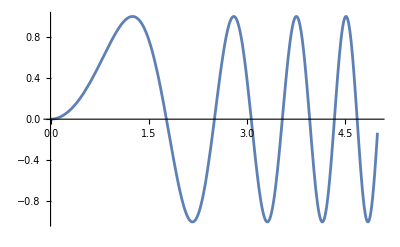

```mathematica
Plot[Sin[x^2],{x,0,5}]
```

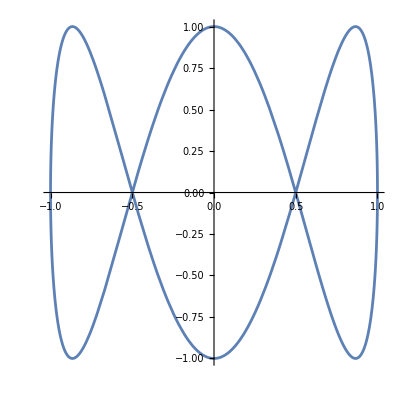

```mathematica
ParametricPlot[{Cos[x],Sin[3x]},{x,0,2Pi}]
```

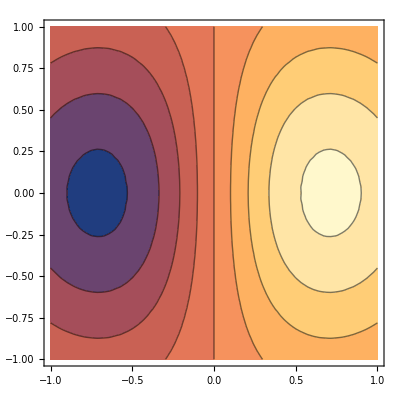

-Graphics-

```mathematica
ContourPlot[x Exp[-x^2-y^2],{x,-1,1},{y,-1,1}]
DensityPlot[x Exp[-x^2-y^2],{x,-1,1},{y,-1,1}]
```

```mathematica
integral=Integrate[x/(x^3-1),x]
simplified=Simplify[D[integral,x]]
```

ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

x/(-1+x^3)

```mathematica
Integrate[Sin[x]^2 Cos[x]^3/x,{x,0,Infinity}]
```

Log[15]/16

```mathematica
Integrate[Sin[Sin[x]],{x,0,1}]
```

∫_0^1 Sin[Sin[x]]ⅆx

```mathematica
N[%]
```

0.430606

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,1}]
```

0.430606

```mathematica
s=Solve[a x^2+b x+c==0,x]
backSubstitution=Simplify[a x^2+b x+c/. s]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

{0,0}

```mathematica
solutions=Solve[x^3-x+1==0,x]
numericSolutions=N[x/. solutions]
```

{{x→Root-1.32Root[1-#1+#1^3&,1]-1.324717957244746},{x→Root0.662-0.562 ⅈRoot[1-#1+#1^3&,2]0.662358978622373},{x→Root0.662+0.562 ⅈRoot[1-#1+#1^3&,3]0.662358978622373}}

{-1.32472,0.662359-0.56228 ⅈ,0.662359+0.56228 ⅈ}

```mathematica
mat={{3.5, 7.2}, {-2.4, 6.4}}
inverse=Inverse[mat]
eigenvalues=Eigenvalues[mat]
```

{{3.5,7.2},{-2.4,6.4}}

{{0.16129,-0.181452},{0.0604839,0.0882056}}

{4.95+3.89583 ⅈ,4.95-3.89583 ⅈ}

```mathematica
mat={{a,b,c},{d,e,f},{g,h,i}}
minv=Inverse[mat]
result=Simplify[minv.mat]
```

{{a,b,c},{d,e,f},{g,h,i}}

{{(-f h+e i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(c h-b i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(-c e+b f)/(-c e g+b f g+c d h-a f h-b d i+a e i)},{(f g-d i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(-c g+a i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(c d-a f)/(-c e g+b f g+c d h-a f h-b d i+a e i)},{(-e g+d h)/(-c e g+b f g+c d h-a f h-b d i+a e i),(b g-a h)/(-c e g+b f g+c d h-a f h-b d i+a e i),(-b d+a e)/(-c e g+b f g+c d h-a f h-b d i+a e i)}}

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
rand=RandomReal[{-1,1},{3,3}]
rand[[2,2]]=x;
inverse=Inverse[rand]
numericalInverse=inverse/. x->1
```

{{0.457812,-0.527412,0.498019},{0.0156287,0.144422,0.149473},{0.151936,-0.291652,-0.895679}}

{{(0.0435943-0.895679 x)/(-0.00167269-0.48572 x),-0.617641/(-0.00167269-0.48572 x),(-0.0788342-0.498019 x)/(-0.00167269-0.48572 x)},{0.0367088/(-0.00167269-0.48572 x),-0.48572/(-0.00167269-0.48572 x),-0.0606474/(-0.00167269-0.48572 x)},{(-0.00455815-0.151936 x)/(-0.00167269-0.48572 x),0.053389/(-0.00167269-0.48572 x),(0.00824278+0.457812 x)/(-0.00167269-0.48572 x)}}

{{1.74825,1.26723,1.18355},{-0.0753166,0.996568,0.124432},{0.321085,-0.10954,-0.956221}}

```mathematica
is=Table[i!,{i,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
data=N[Log[is]]
```

{0.,0.693147,1.79176,3.17805,4.78749,6.57925,8.52516,10.6046,12.8018,15.1044}

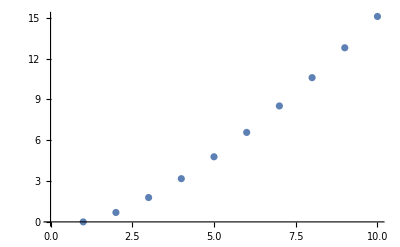

```mathematica
p1=ListPlot[data]
```

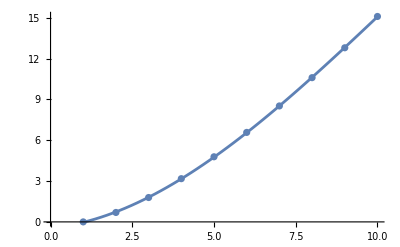

```mathematica
fit=Fit[data,{1,x,x^2,x^3},x];
p2=Plot[fit,{x,1,10},PlotRange->All];
Show[p1,p2]
```

```mathematica
Animate[Plot[Sin[a x],{x,-Pi,Pi},PlotRange->{-1,1}],{a,1,5}]
Animate[Plot3D[Sin[a x] Cos[b y],{x,-Pi,Pi},{y,-Pi,Pi},PlotRange->{-1,1}],{a,1,5},{b,1,5}]
```

```mathematica
img=Import["/Users/qiu_nangong/Documents/GitHub/Mathematica/image.png"]; (*Load the image*)
grayImg=ColorConvert[img,"Grayscale"]; (*Convert to grayscale*)
blurredImg=GaussianFilter[grayImg,5]; (*Apply Gaussian blur*)
adjustedImg=ImageAdjust[blurredImg,{0.5,0.5}]; (*Adjust brightness and contrast*)
edges=EdgeDetect[adjustedImg]; (*Perform edge detection*)
```

```mathematica
%116
```

-Graphics-